```mathematica
(*   Diffraction for a single slit
-Graphics-*}
```

Syntax::bktmop: Expression "…" has no opening ""{"""".

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
d=1.0E-7
```

-4.28172

```mathematica
β= 2*Pi*d*Sin[theta]
```

-26.9028 Sin[theta]

```mathematica
Diffraction:=Sin[β/2]/(β/2)
```

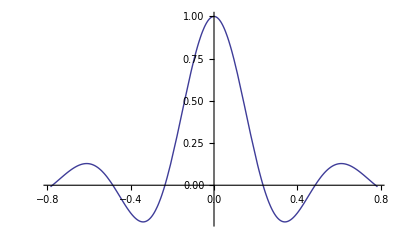

```mathematica
Plot[Diffraction, {theta,-Pi/4,Pi/4},PlotRange->All]
```

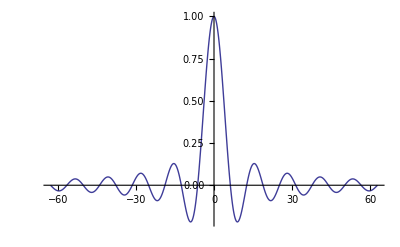

```mathematica
Plot[Diffraction, {β,-20*Pi,20*Pi},PlotRange->All]
```

```mathematica
(*  INTENSITY = Diffraction function Squared   *)
```

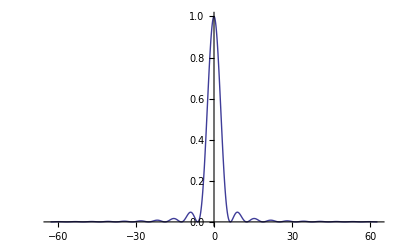

```mathematica
Plot[Diffraction^2, {β,-20*Pi,20*Pi},PlotRange->All]
```

```mathematica
AreaTotal =NIntegrate  [ Diffraction^2,{β,0,20*Pi}]
```

3.10978

```mathematica
Area90= NIntegrate  [ Diffraction^2,{β,0,2*Pi}]
```

2.8363

```mathematica
100*Area90/AreaTotal
```

91.206

```mathematica
(*-Graphics-=   2π 
   thus   λ = a sin(θ) *)
```

```mathematica
(* Application   Slit = 400 nm *)
```

```mathematica
d= 400*10^-9
```

1/2500000

```mathematica
ThetaCal := ArcSin[λ/d]
```

```mathematica
ArcSin[0]
```

0

```mathematica
ArcSin[1]
```

π/2

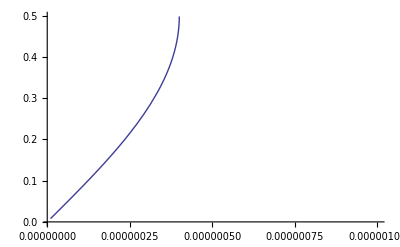

```mathematica
Plot [ArcSin[λ/d]/Pi, {λ,10*10^-9,1000*10^-9}]
```